Nearest point in a parametric plot of the delta config space

### Testing RegionMember function on polygon

```mathematica
Manipulate[With[{f=BSplineFunction[{{0.5,0.05},{1.05,0.7},{0.4,1.5},{-1.15,0.85},{-0.75,0.02},{-0.93,-1},{0.2,-1.3},{1.05,-0.83}},SplineClosed->True]},reg=Polygon[Table[f[t],{t,0,.99,0.01}]];
rm=RegionMember[reg];];
Column[{Graphics[{Point[p],EdgeForm[{Red,Thick}],Yellow,reg},PlotRange->Table[{-2,2},{2}](*,Point[RegionNearest[reg,p]],Blue*)],Row[{"Region Member: ",rm[p]}]}],{{p,{0.5,0.5}},Locator}]
```

### Testing Nearest REgion function on polygon

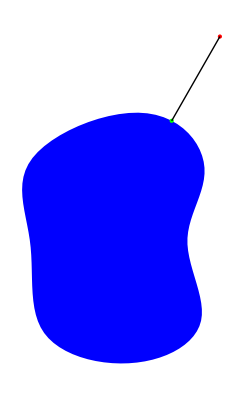

```mathematica
p={1,2};
pn=RegionNearest[reg,p];
Graphics[{Blue,reg,Red,PointSize[Large],Point[p],Green,Point[pn],Black,Line[{pn,p}]}]
```

### PLotting the actual region (parametric form!)

```mathematica
clipCircle[p_,ϵ_]:=If[Norm[p]>1/2-ϵ,(1/2-ϵ)p/Norm[p],p]; (*keeps robots inside of circle of radius 1/2-ϵ*)
ϵ = 1/1000;
reg2;
Manipulate[Module[{thickness = 0.005,
d (*distance between robots*),
θ(*angle between the two particles*),
α(*anglular arc unreachable by robots*),
r = 1/40 (*radius of start and end markers*),
(*perpendicular distance: maximum height of chord to boundary *) pr,
(*reachable angle*) γ,
(*angle to collision*) ψ,
(*left robot*) ps1,pe1,
(*right robot*) ps2,pe2,
(*collision point*)pcol1,
c1=Blue,c2 =Magenta},
s1=clipCircle[s1,ϵ];
e1=clipCircle[e1,ϵ];
s2=clipCircle[s2,ϵ];
e2=clipCircle[e2,ϵ];

{ps1 ,pe1,ps2,pe2} = {s1,e1,s2,e2};
If[Norm[col1]≠ 1/2,col1 =col1/(2 Norm[col1])];

{ps1 ,ps2,pcol1} = {s1,s2,col1};
d = Norm[ps1-ps2];(*distance between robots*)
θ = ArcTan[ps1⟦1⟧-ps2⟦1⟧,ps1⟦2⟧-ps2⟦2⟧]; (*angle between the two particles*)
α = 2 ArcSin[d]; (*anglular arc unreachable by robots*)

ψ =ArcTan[col1⟦1⟧,col1⟦2⟧];(*angle to collision*)
pr = 2 Abs[ps1.col1-ps2.col1]; (*perpendicular distance: *)
γ = ArcCos[(1/2-pr)/(1/2)];(*reachable angle for other robot after first robot collides*)
Graphics[{
(*workspace*)
{Darker[Red], Disk[{0,0},1.025/2]},
{Lighter[Gray,0.8], Disk[{0,0},1/2]},
{White, Disk[{0,0},1/2-ϵ]},
{Lighter[Gray,0.8], Disk[ps2,ϵ]},
PointSize[0.01],
Arrowheads[.03],
{(*wall collision points*)Thickness[3 thickness],c2,Circle[{0,0},1/2,{θ+α/2+π/2,θ-α/2-π/2+2π}]},
{(*wall collision points*)Thickness[3 thickness],c1,Circle[{0,0},1/2,{θ-α/2+π/2,θ+α/2-π/2}]},

 {(*reachable regions when robot 2 hits first: try many collision points*)
Module[{ψa ,pra,γa,cola},
Table[
ψa=θ+α/2+π/2+c (π-α)/20;
cola = 1/2{Cos[ψa ],Sin[ψa ]};(*collision point for robot 2 -- where it hits the circular boundary*)
pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance: maximum height of chord to boundary *)
γa= ArcCos[(1/2-pra)/(1/2)];(*reachable angle for other robot after first robot collides*)
{Hue[ψa/(2π)],Point[cola],
{(*draw the chord of reachable locations by robot 1 after robot 2 hits cola*)
Opacity[0.05],Polygon[Table[1/2{Cos[a],Sin[a]},{a,ψa -γa ,ψa +γa,γa/20  (*approximate a chord of a circle by taking many points*)}]]},
Line[{1/2{Cos[ψa -γa],Sin[ψa-γa]},1/2{Cos[ψa +γa],Sin[ψa+γa]}}]},
{c,0,hits }]]
},
 {(*reachable regions when robot 1 hits first*)
Module[{ψa ,pra,γa,cola,c},
Table[
ψa=θ+α/2-π/2+c(π-α)/20;
cola = 1/2{Cos[ψa ],Sin[ψa ]};
pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance*)
γa= ArcCos[(1/2-pra)/(1/2)];
{Hue[ψa/(2π)],Point[cola],
{Opacity[0.05],EdgeForm[Directive[Hue[ψa/(2π)]]],Polygon[Table[1/2{Cos[a],Sin[a]},{a,ψa -γa ,ψa +γa,γa/20}]]},
(*draw the chord in a solid (non-transparent) line*)
Line[{1/2{Cos[ψa -γa],Sin[ψa-γa]},1/2{Cos[ψa +γa],Sin[ψa+γa]}}]},
{c,0,hits}]]
},
(*starting poses, dashed line from start to end*)
{c1,Thickness[thickness],{ Opacity[.3],Dashed,Arrow[{ps1,pe1}]},Point@ps1,EdgeForm[Directive[c1,Thickness[thickness]]],FaceForm[None],Rectangle[ps1-2/3r {1,1},ps1+2/3r{1,1}],Circle[pe1,r]},
{c2,Thickness[thickness],{ Opacity[.3],Dashed,Arrow[{ps2,pe2}]},Point@ps2,EdgeForm[Directive[c2,Thickness[thickness]]],FaceForm[None],Rectangle[ps2-2/3r {1,1},ps2+2/3r{1,1}], Circle[pe2,r]},

Inset[Module[{ψa ,pra,γa,cola,γa2},cola = 1/2{Cos[ψa ],Sin[ψa ]}; (*collision point*)

pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance*)
γa= ArcCos[(1/2-pra)/(1/2)];(*reachable angle for other robot after first robot collides*)
(*reg2=Polygon[Join[
Table[cola-1/2{Cos[a+θ+α/2+π/2],Sin[a+θ+α/2+π/2]},{a,-γa ,+γa,γa/10}],
Table[cola-1/2{Cos[a+θ-α/2+3/2π ],Sin[a+θ-α/2+3/2π ]},{a,-γa ,+γa,γa/10}]
]];*)
(*
reg=Polygon[
ψa=θ+α/2+π/2;
Table[cola-1/2{Cos[a],Sin[a]},{a,ψa -γa ,ψa +γa,γa/10}]
];*)

ParametricPlot[{cola-1/2{Cos[a],Sin[a]}}, {ψa,θ+α/2+π/2,θ-α/2+3/2π},{a,ψa -γa ,ψa +γa},PlotRange-> {{-1,1},{-1,1}},FrameLabel->{"Δx","Δ y"},LabelStyle->Directive[Black,Bold,Large],ImageSize->400, Epilog-> {Circle[{0,0},1-2ϵ],

(*THIS IS HORRIBLY COMPLICATED.  SURELY IT SIMPLIFIES.  PLEASE SIMPLIFY IT*)
γa2= ArcCos[(1/2-pra)/(1/2)]/.{ψa-> θ+α/2+π/2};Thick,Text[γa2,{0,0}],
Pink,Line[Table[ 1/2{Cos[θ+α/2+π/2 ],Sin[θ+α/2+π/2 ]}-1/2{Cos[a2+θ+α/2+π/2],Sin[a2+θ+α/2+π/2]},{a2,-γa2,+γa2,γa2/5}]],

γa2= ArcCos[(1/2-pra)/(1/2)]/.{ψa-> θ-α/2+3π/2};Thick,Text[γa2,{0,0}],
Red,Line[Table[ 1/2{Cos[θ-α/2+3π/2 ],Sin[θ-α/2+3π/2 ]}-1/2{Cos[a2+θ-α/2+3π/2],Sin[a2+θ-α/2+3π/2]},{a2,-γa2,+γa2,γa2/5}]],


Green,Line[Table[  1/2{Cos[ψa ],Sin[ψa ]}-1/2{Cos[ψa -γa],Sin[ψa -γa]},{ψa,θ+α/2+π/2,θ-α/2+3/2π,(π-α)/20}]],
Brown,Line[Table[  1/2{Cos[ψa ],Sin[ψa ]}-1/2{Cos[ψa +γa],Sin[ψa +γa]},{ψa,θ+α/2+π/2,θ-α/2+3/2π,(π-α)/20}]],

(*goal deltas*)
Red,
Disk[pe2-pe1,2r],Text[Style[StringForm["Δg"],FontSize->24,Black,FontFamily-> "Times"],pe2-pe1-{.1,.1}],
(*current deltas*)
Darker[Green],Rectangle[ps2-ps1-4/3r {1,1},ps2-ps1+4/3r{1,1}],Text[Style[StringForm["Δr"],FontSize->24,Black,FontFamily-> "Times"],{ps2⟦1⟧-ps1⟦1⟧+ 0.1,ps2⟦2⟧-ps1⟦2⟧+0.1}]}]],{1.2,0}]
},ImageSize->800,PlotRange->{{-0.55,1.75},{-.55,.55}}]],
Row[{Control@{{progress,1,"progress"},0,1,1/420,Slider,Appearance->"Labeled"},
Control@{{ϵ,1/1000,"ϵ"},1/1000,1/5,1/1000,Slider,Appearance->"Labeled"}}],
Control@{{hits,0,"hits"},0,21,1,Slider,Appearance->"Labeled"},
{{s1,{0.0,0.0}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None},
{{s2,{0.2,0.4}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None},
{{col1,{0.2,0.4}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None},
{{e1,{0.05,0.35}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None},
{{e2,{-0.33,0.26}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None}
, SaveDefinitions->True]
```

```mathematica
Graphics[{Blue,EdgeForm->Red,reg2}]
```

-Graphics-

```mathematica
Inset[Module[{ψa ,pra,γa,cola,α ,r = 1/40 (*radius of start and end markers*),
d = Norm[ps1-ps2];(*distance between robots*)
θ = ArcTan[ps1⟦1⟧-ps2⟦1⟧,ps1⟦2⟧-ps2⟦2⟧]; (*angle between the two particles*)
},
α = 2 ArcSin[d]; (*anglular arc unreachable by robots*)

cola = 1/2{Cos[ψa ],Sin[ψa ]}; (*collision point*)

pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance*)
γa= ArcCos[(1/2-pra)/(1/2)];(*reachable angle for other robot after first robot collides*)
reg=Polygon[Join[
ψa=θ+α/2+π/2;
Table[{cola-1/2{Cos[a],Sin[a]}},{a,ψa -γa ,ψa +γa}],
ψa=θ-α/2+3/2π;
]];



ParametricPlot[{cola-1/2{Cos[a],Sin[a]}}, {ψa,θ+α/2+π/2,θ-α/2+3/2π},{a,ψa -γa ,ψa +γa},PlotRange-> {{-1,1},{-1,1}},FrameLabel->{"Δx","Δ y"},LabelStyle->Directive[Black,Bold,Large],ImageSize->400, Epilog-> {Circle[{0,0},1-2ϵ],(*goal deltas*)
Red,
Disk[pe2-pe1,2r],Text[Style[StringForm["Δg"],FontSize->24,Black,FontFamily-> "Times"],pe2-pe1-{.1,.1}],
(*current deltas*)
Darker[Green],Rectangle[ps2-ps1-4/3r {1,1},ps2-ps1+4/3r{1,1}],Text[Style[StringForm["Δr"],FontSize->24,Black,FontFamily-> "Times"],{ps2⟦1⟧-ps1⟦1⟧+ 0.1,ps2⟦2⟧-ps1⟦2⟧+0.1}]}]],{1.2,0}]
```

Module::lvsym: Local variable specification {ψa, pra, γa, cola, α, r = 1/40, d = Norm[ps1 - ps2] ; θ = ArcTan[ps1 ⟦ 1 ⟧ - ps2 ⟦ 1 ⟧, ps1 ⟦ 2 ⟧ - ps2 ⟦ 2 ⟧] ;} contains d = Norm[ps1 - ps2] ; θ = ArcTan[ps1 ⟦ 1 ⟧ - ps2 ⟦ 1 ⟧, ps1 ⟦ 2 ⟧ - ps2 ⟦ 2 ⟧] ;, which is not a symbol or an assignment to a symbol.

Inset[Module[{ψa,pra,γa,cola,α,r=1/40,d=Norm[ps1-ps2];θ=ArcTan[ps1⟦1⟧-ps2⟦1⟧,ps1⟦2⟧-ps2⟦2⟧];},α=2 ArcSin[d];cola=1/2 {Cos[ψa],Sin[ψa]};pra=2 Abs[ps1.cola-ps2.cola];γa=ArcCos[(1/2-pra)/(1/2)];reg=Polygon[Join[ψa=θ+α/2+π/2;Table[{cola-1/2 {Cos[a],Sin[a]}},{a,ψa-γa,ψa+γa}],ψa=θ-α/2+(3 π)/2;]];ParametricPlot[{cola-1/2 {Cos[a],Sin[a]}},{ψa,θ+α/2+π/2,θ-α/2+(3 π)/2},{a,ψa-γa,ψa+γa},PlotRange→{{-1,1},{-1,1}},FrameLabel→{Δx,Δ y},LabelStyle→Directive[Black,Bold,Large],ImageSize→400,Epilog→{Circle[{0,0},1-2 ϵ],Red,Disk[pe2-pe1,2 r],Text[Style[Δg,FontSize→24,Black,FontFamily→Times],pe2-pe1-{0.1,0.1}],Darker[Green],Rectangle[ps2-ps1-4/3 r {1,1},ps2-ps1+4/3 r {1,1}],Text[Style[Δr,FontSize→24,Black,FontFamily→Times],{ps2⟦1⟧-ps1⟦1⟧+0.1,ps2⟦2⟧-ps1⟦2⟧+0.1}]}]],{1.2,0}]